```mathematica
ν[m_][i_][T[i_,j_]]:=(-1)^j qi[m]^-1(
If[j>0,(-1)^(m-i)qi[i+j]T[i+1,j-1],0]+
If[i+j>m/2,qi[2i+j-m/2]T[i+1,j-2],0]+
If[i+j<m/2,qi[j+m/2]T[i+1,j],0]
)
```

```mathematica
ν[m_][i_][a_ t_T]:=a ν[m][i][t]
ν[m_][i_][X_Plus]:=ν[m][i]/@X
```

```mathematica
resμ[m_][i_,z_][T[i_,j_]]:=Sum[
(-1)^i(m-2i)^-1 qi[m]^-1(Sum[ζ[m-2i]^(ℓ(j-jp))(qi[m-i] ζ[m-2i]^-ℓ+(-1)^m qi[i] ζ[m-2i]^ℓ)^-1,{ℓ,0,m-2i-1}])T[i,jp]
,{jp,0,m-2i-1}]
```

```mathematica
resμ[m_][i_,z_][a_ t_T]:=a resμ[m][i,z][t]
resμ[m_][i_,z_][X_Plus]:=resμ[m][i,z]/@X
resμ[m_][i_,z_][X_Times]:=resμ[m][i,z][Expand[X]]
```

```mathematica
X[m_,ω_][0]:=Sum[ω^-j T[0,j],{j,0,m-1}]
```

```mathematica
X[m_,ω_][i_]:=-resμ[m][i,ω][ν[m][i-1][X[m,ω][i-1]]]
```

```mathematica
With[{m=10,ω=-1},
X[m,ω][0]
]
```

T[0,0]-T[0,1]+T[0,2]-T[0,3]+T[0,4]-T[0,5]+T[0,6]-T[0,7]+T[0,8]-T[0,9]

```mathematica
ζ/:ζ[n_]^m_/;m≥n:=ζ[n]^Mod[m,n]
```

```mathematica
ζ/:ζ[8]^(n_?EvenQ):=ⅈ^(n/2)
ζ/:ζ[8]^(n_?OddQ):=ⅈ^((n-1)/2)ζ[8]
```

```mathematica
qi[k_]:=(q^k-q^-k)/(q-q^-1)
```

```mathematica
r[j_]/;j>1:=r[Mod[j,2]]
```

```mathematica
a[m_][σ_,ω_]:=Together[X[m,ω][1]/.T[1,j_]:>σ^j r[j+1]]
```

```mathematica
a[10][ⅈ,-1]
```

(2 q^18 (ⅈ r[0]+ⅈ q^2 r[0]+ⅈ q^4 r[0]+ⅈ q^6 r[0]+ⅈ q^8 r[0]+q r[1]+q^3 r[1]+q^5 r[1]+q^7 r[1]))/((1+q^2)^4 (1+q^4) (1-q^2+q^4-q^6+q^8)^2 (1+q^2+q^4+q^6+q^8)^2)

```mathematica
a[10][ⅈ,1]
```

0

```mathematica
a[10][ⅈ,ⅈ]/._r:>1//Together
```

((1+ⅈ) q^18 (ⅈ+ⅈ q^2+ⅈ q^4+q^5+ⅈ q^6+q^7+ⅈ q^8+ⅈ q^10+ⅈ q^12))/((1+q^2)^4 (1+q^4) (1-q+q^2-q^3+q^4) (1+q+q^2+q^3+q^4)^2 (1-q^2+q^4-q^6+q^8)^3)

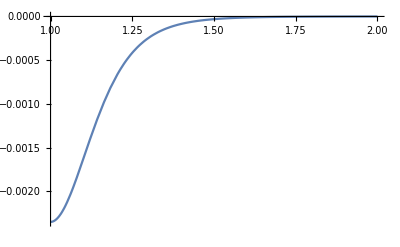

```mathematica
Plot[Evaluate[Re[a[10][ⅈ,Exp[2π ⅈ/8]]/._r:>1]],{q,1,2}]
```

```mathematica
b[n_][σ_,ω_]:=1/qi[2n+2]∑_(j=0)^n (ω^-j+ω^(-j+n+1))((-1)^j(σ^j qi[2n+2-j]+σ^(j-2)qi[j])r[j]+(-1)^(n+j+1)(σ^(j+1)qi[n+1-j]+σ^(j-1)qi[n+1+j])r[j+1])
```

```mathematica
Z[n_,σ_,ω_]:=1/qi[2n+2] a[2n+2][σ,ω](q^(2n+2)+q^(-2n-2)-σ^2-σ^-2)+b[n][σ,ω]
```

```mathematica
Z[4,ⅈ,1]/.{r[0]->1,r[1]->qi[4+2]/qi[4]}//Together
```

(2 (1-q^2+q^4-q^6+q^8))/(1+q^2+q^4+q^6+q^8)

```mathematica
Solve[%==0,q]
```

{{q→-(-1)^(1/10)},{q→(-1)^(1/10)},{q→-(-1)^(3/10)},{q→(-1)^(3/10)},{q→-(-1)^(7/10)},{q→(-1)^(7/10)},{q→-(-1)^(9/10)},{q→(-1)^(9/10)}}

```mathematica
Z[4,ⅈ,ⅈ]/.{r[0]->1,r[1]->qi[4+2]/qi[4]}//Together
```

-(((1-ⅈ) ((1+ⅈ)-(1+2 ⅈ) q+(5+6 ⅈ) q^2-(6+10 ⅈ) q^3+(16+20 ⅈ) q^4-(19+30 ⅈ) q^5+(38+48 ⅈ) q^6-(43+66 ⅈ) q^7+(72+92 ⅈ) q^8-(78+118 ⅈ) q^9+(117+150 ⅈ) q^10-(121+182 ⅈ) q^11+(169+217 ⅈ) q^12-(168+252 ⅈ) q^13+(224+288 ⅈ) q^14-(216+324 ⅈ) q^15+(280+360 ⅈ) q^16-(265+396 ⅈ) q^17+(338+432 ⅈ) q^18-(315+468 ⅈ) q^19+(394+502 ⅈ) q^20-(363+537 ⅈ) q^21+(444+565 ⅈ) q^22-(402+594 ⅈ) q^23+(478+611 ⅈ) q^24-(424+628 ⅈ) q^25+(490+628 ⅈ) q^26-(424+628 ⅈ) q^27+(478+611 ⅈ) q^28-(402+594 ⅈ) q^29+(444+565 ⅈ) q^30-(363+537 ⅈ) q^31+(394+502 ⅈ) q^32-(315+468 ⅈ) q^33+(338+432 ⅈ) q^34-(265+396 ⅈ) q^35+(280+360 ⅈ) q^36-(216+324 ⅈ) q^37+(224+288 ⅈ) q^38-(168+252 ⅈ) q^39+(169+217 ⅈ) q^40-(121+182 ⅈ) q^41+(117+150 ⅈ) q^42-(78+118 ⅈ) q^43+(72+92 ⅈ) q^44-(43+66 ⅈ) q^45+(38+48 ⅈ) q^46-(19+30 ⅈ) q^47+(16+20 ⅈ) q^48-(6+10 ⅈ) q^49+(5+6 ⅈ) q^50-(1+2 ⅈ) q^51+(1+ⅈ) q^52))/(q (1+q^2)^3 (1+q^4)^2 (1-q+q^2-q^3+q^4)^3 (1+q+q^2+q^3+q^4)^2 (1-q^2+q^4-q^6+q^8)^2))

```mathematica
q+q^-1/.NSolve[%]
```

{0.302778+0.438849 ⅈ,-0.890405+0.283842 ⅈ,-1.16028-0.249708 ⅈ,0.49123+0.232952 ⅈ,0.00574359-0.213766 ⅈ,1.25025-0.152979 ⅈ,1.89582+0.0614876 ⅈ,-0.355775+0.159356 ⅈ,-0.687177-0.143445 ⅈ,0.709281-0.129635 ⅈ,-1.42571+0.0946724 ⅈ,1.41789+0.0853662 ⅈ,-1.58925-0.0735732 ⅈ,1.59282-0.0683171 ⅈ,1.08392+0.0892311 ⅈ,-1.2642-0.0772869 ⅈ,-1.06538+0.0741919 ⅈ,-1.66+0.0327401 ⅈ,1.66456+0.0323116 ⅈ,1.90072+0.01303 ⅈ,-0.390712+0.0380248 ⅈ,-1.90453-0.0108023 ⅈ,-1.90103+0.0105542 ⅈ,1.90387-0.00948796 ⅈ,0.323322-0.0133403 ⅈ,1.25223-0.00426865 ⅈ,1.25223-0.00426865 ⅈ,0.323322-0.0133403 ⅈ,1.90387-0.00948796 ⅈ,-1.90103+0.0105542 ⅈ,-1.90453-0.0108023 ⅈ,-0.390712+0.0380248 ⅈ,1.90072+0.01303 ⅈ,1.66456+0.0323116 ⅈ,-1.66+0.0327401 ⅈ,-1.06538+0.0741919 ⅈ,-1.2642-0.0772869 ⅈ,1.08392+0.0892311 ⅈ,1.59282-0.0683171 ⅈ,-1.58925-0.0735732 ⅈ,1.41789+0.0853662 ⅈ,-1.42571+0.0946724 ⅈ,0.709281-0.129635 ⅈ,-0.687177-0.143445 ⅈ,-0.355775+0.159356 ⅈ,1.89582+0.0614876 ⅈ,1.25025-0.152979 ⅈ,0.00574359-0.213766 ⅈ,0.49123+0.232952 ⅈ,-1.16028-0.249708 ⅈ,-0.890405+0.283842 ⅈ,0.302778+0.438849 ⅈ}